```mathematica
Needs["NumericalCalculus`"];
```

```mathematica
min= -0.9;  max= 5; step=0.0005;   MAX=10^10;
```

```mathematica
Subscript[Ω, m0]=0.315;  H0.b2=(67.37)^2; Subscript[Ω, Λ0]= 0.6847; Subscript[Ω, r0]=  3 10^(-4);
```

```mathematica
β=0.45; α=0.93;
```

```mathematica
Subscript[Δ, 1]=0.0; Subscript[Δ, 2]=3 10^-3; Subscript[Δ, 3]=7 10^-3; Subscript[Δ, 4]=1 10^-2; Subscript[Δ, 5]=2 10^-2;     legends={"Δ= 0","Δ= 3 x10^-3","Δ= 7 x10^-3","Δ= 10 x10^-3","Δ= 20 x10^-3","ΛCDM"};
```

------------------------//-------------------------------------------------//-------------------------------------------------------------//---------------------------------------------------------//--------------------------------

```mathematica
HΛCDM[z_]:= Sqrt[H0.b2(Subscript[Ω, m0](1+z)^3 + Subscript[Ω, r0](1+z)^4  + Subscript[Ω, Λ0])];
```

```mathematica
Friedmann= (1+z)(β/2) y'[z] - α y[z]  + (  y[z] -Subscript[Ω, m0] H0.b2(1+z)^3 -Subscript[Ω, r0] H0.b2(1+z)^4  )^(2/(2-Δ)) ==0
```

-0.93 y[z]+(-1429.7 (1+z)^3-1.36162 (1+z)^4+y[z])^(2/(2-Δ))+0.225 (1+z) y'[z]==0

```mathematica
Solucion1=  NDSolveValue[{Friedmann, y[0]==H0.b2}/. {Δ-> Subscript[Δ, 1] } ,y[z],{z,min,MAX},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->40,PrecisionGoal->12]; 
Solucion2=  NDSolveValue[{Friedmann, y[0]==H0.b2}/. {Δ->Subscript[Δ, 2] } ,y[z],{z,min,MAX},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->40,PrecisionGoal->12]; 
Solucion3=  NDSolveValue[{Friedmann, y[0]==H0.b2}/. {Δ-> Subscript[Δ, 3] } ,y[z],{z,min,MAX},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->40,PrecisionGoal->12];
```

```mathematica
Solucion4=  NDSolveValue[{Friedmann, y[0]==H0.b2}/. {Δ-> Subscript[Δ, 4] } ,y[z],{z,min,MAX},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->40,PrecisionGoal->12];
```

```mathematica
Solucion5=  NDSolveValue[{Friedmann, y[0]==H0.b2}/. {Δ-> Subscript[Δ, 5] } ,y[z],{z,min,MAX},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->40,PrecisionGoal->12];
```

------------------------//-------------------------------------------------//-------------------------------------------------------------//---------------------------------------------------------//--------------------------------

```mathematica
plot={Sqrt[Solucion1],Sqrt[Solucion2],Sqrt[Solucion3],Sqrt[Solucion4],Sqrt[Solucion5]};
```

```mathematica
styles={Directive[Line],Directive[DotDashed],Directive[Dashing[{0.008}]],Directive[Line],Directive[DotDashed],Directive[Dashing[{0.008}],Black]}; title="β=0.45   α=0.93";
```

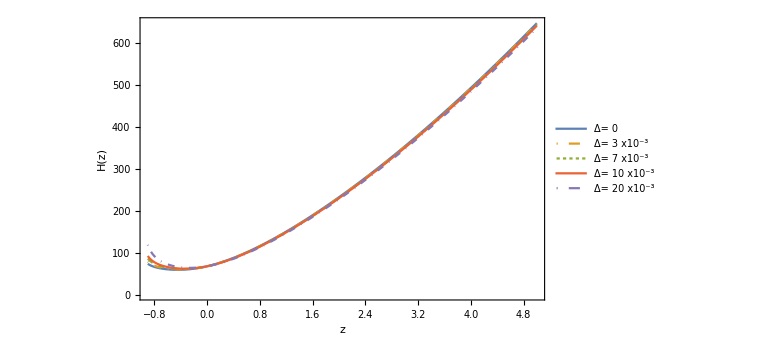

```mathematica
plotZvsH=Plot[plot,{z,min,max} ,PlotRange-> {0,Automatic},PlotLegends-> Placed[legends,{0.85,0.25}],PlotStyle->styles,LabelStyle->Directive[Black,Bold,10],ImageSize->Large,Frame->True, FrameLabel->{{"H(z)",""},{z,title}}]
```

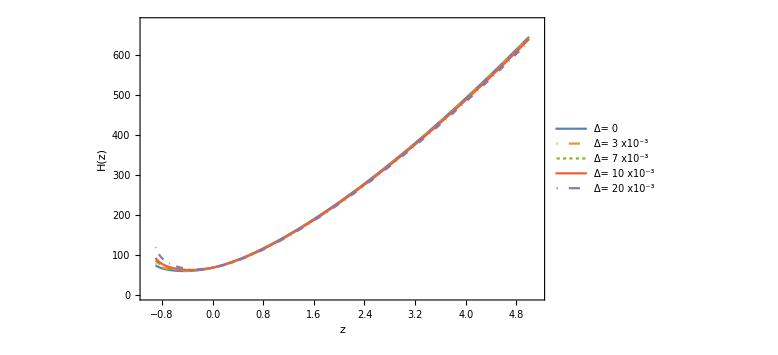

-Graphics-

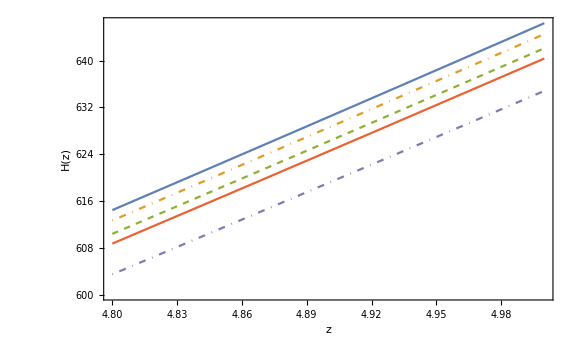

```mathematica
Plot[plot,{z,4.8,5} ,PlotRange-> {600,Automatic},PlotStyle->styles,LabelStyle->Directive[Black,Bold,10],ImageSize->Large,Frame->True, FrameLabel->{{"H(z)",""},{z,""}}]
```

```mathematica
plotZvsH=Plot[{plot,HΛCDM[z]},{z,min,MAX} ,PlotRange-> {0,Automatic},PlotLegends-> Placed[legends,{0.85,0.25}],PlotStyle->styles,LabelStyle->Directive[Black,Bold,11],ImageSize->Large,Frame->True, FrameLabel->{{"H(z)",""},{z,title}}]
```

-Graphics-

-Graphics-

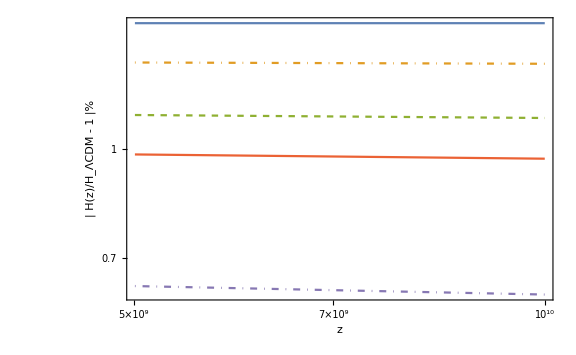

```mathematica
plot2={Abs[Sqrt[Solucion1]-HΛCDM[z]]/Sqrt[Solucion1]*100,Abs[Sqrt[Solucion2]-HΛCDM[z]]/Sqrt[Solucion2]*100,Abs[Sqrt[Solucion3]-HΛCDM[z]]/Sqrt[Solucion3]*100,Abs[Sqrt[Solucion4]-HΛCDM[z]]/Sqrt[Solucion4]*100,Abs[Sqrt[Solucion5]-HΛCDM[z]]/Sqrt[Solucion5]*100};

plotZvsH=LogLogPlot[plot2,{z,min,MAX}, AxesLabel->{"z","Error %"} ,PlotRange-> {0,Automatic},PlotStyle->styles,LabelStyle->Directive[Black,Bold,11],ImageSize->Large,Frame->True, FrameLabel->{{"| H(z)/H_ΛCDM - 1 |%",""},{z,"Con respecto a Λ-CDM"}}]
```

```mathematica
dataZvsH=Cases[plotZvsH,Line[{x__}]:>x,All]; Export["output2.csv",dataZvsH//Prepend[{"z","H(z)"}]]; Z= Range[min,max,step];
```

```mathematica
H21=Solucion1[[0]];            H22=Solucion2[[0]];                H23=Solucion3[[0]];    H24=Solucion4[[0]];  H25=Solucion5[[0]];
```

------------------------//-------------------------------------------------//-------------------------------------------------------------//---------------------------------------------------------//--------------------------------

```mathematica
dH21dz= ND[H21[z],z,Z,WorkingPrecision->40,Terms->10]; dH22dz= ND[H22[z],z,Z,WorkingPrecision->40,Terms->10]; dH23dz= ND[H23[z],z,Z,WorkingPrecision->40,Terms->10]; dH24dz= ND[H24[z],z,Z,WorkingPrecision->40,Terms->10]; dH25dz= ND[H25[z],z,Z,WorkingPrecision->40,Terms->10];
```

```mathematica
q1=-1+(1/2)(1+Z)dH21dz/(H21[Z]) ; dataZvsq1= Transpose[{Z,q1}];
```

```mathematica
q2=-1+(1/2)(1+Z)dH22dz/(H22[Z]) ; dataZvsq2= Transpose[{Z,q2}];
```

```mathematica
q3=-1+(1/2)(1+Z)dH23dz/(H23[Z]) ; dataZvsq3= Transpose[{Z,q3}];
```

```mathematica
q4=-1+(1/2)(1+Z)dH24dz/(H24[Z]) ; dataZvsq4= Transpose[{Z,q4}];
```

```mathematica
q5=-1+(1/2)(1+Z)dH25dz/(H25[Z]) ; dataZvsq5= Transpose[{Z,q5}];
```

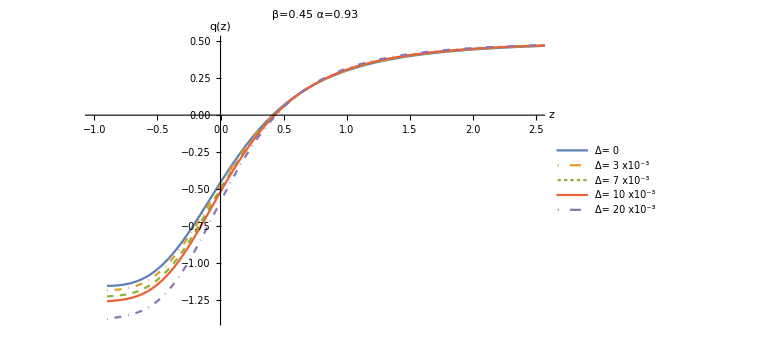

```mathematica
ListLinePlot[{dataZvsq1,dataZvsq2,dataZvsq3,dataZvsq4,dataZvsq5},AxesLabel->{"z","q(z)"},PlotRange->{{-1,2.5},{Automatic,Automatic}},PlotStyle->styles,LabelStyle->Directive[Black,Bold,10],ImageSize->Large,PlotLabel->title,PlotLegends-> Placed[legends,{0.9,0.45}]]
```

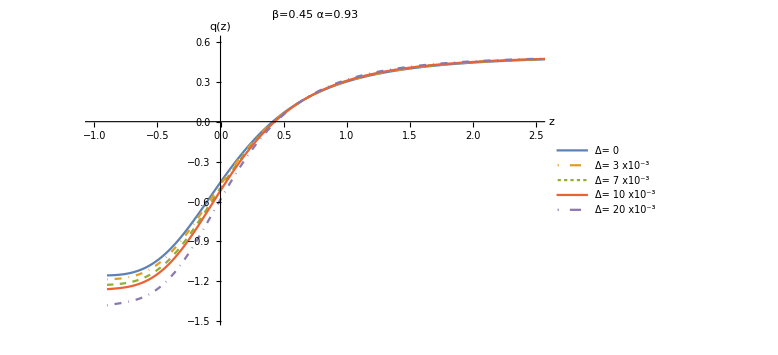

-Graphics-

-Graphics-

-Graphics-

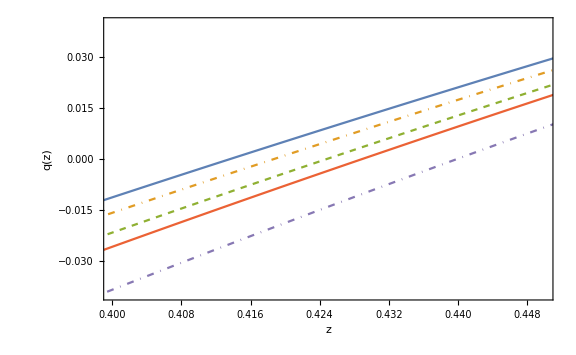

```mathematica
ListLinePlot[{dataZvsq1,dataZvsq2,dataZvsq3,dataZvsq4,dataZvsq5},PlotRange->{{0.4,0.45},{-0.04,0.04}},PlotStyle->styles,LabelStyle->Directive[Black,Bold,11],ImageSize->Large,Frame->True, FrameLabel->{{"q(z)",""},{z,"z_T"}}]
```

------------------------//-------------------------------------------------//-------------------------------------------------------------//---------------------------------------------------------//--------------------------------

```mathematica
Subscript[ρ̃, Λ1]= (1/H0.b2)(α H21[Z] - β (1/2)(1+Z)dH21dz)^(1-(Δ/2))/. {Δ-> Subscript[Δ, 1]}; dataZvsDE1= Transpose[{Z,Subscript[ρ̃, Λ1]}];
```

```mathematica
Subscript[ρ̃, Λ2]= (1/H0.b2)(α H22[Z] - β (1/2)(1+Z)dH22dz)^(1-(Δ/2))/. {Δ-> Subscript[Δ, 2]}; dataZvsDE2= Transpose[{Z,Subscript[ρ̃, Λ2]}];
```

```mathematica
Subscript[ρ̃, Λ3]= (1/H0.b2)(α H23[Z] - β (1/2)(1+Z)dH23dz)^(1-(Δ/2))/. {Δ-> Subscript[Δ, 3]}; dataZvsDE3= Transpose[{Z,Subscript[ρ̃, Λ3]}];
```

```mathematica
Subscript[ρ̃, Λ4]= (1/H0.b2)(α H24[Z] - β (1/2)(1+Z)dH24dz)^(1-(Δ/2))/. {Δ-> Subscript[Δ, 4]}; dataZvsDE4= Transpose[{Z,Subscript[ρ̃, Λ4]}];
```

```mathematica
Subscript[ρ̃, Λ5]= (1/H0.b2)(α H25[Z] - β (1/2)(1+Z)dH25dz)^(1-(Δ/2))/. {Δ-> Subscript[Δ, 5]}; dataZvsDE5= Transpose[{Z,Subscript[ρ̃, Λ5]}];
```

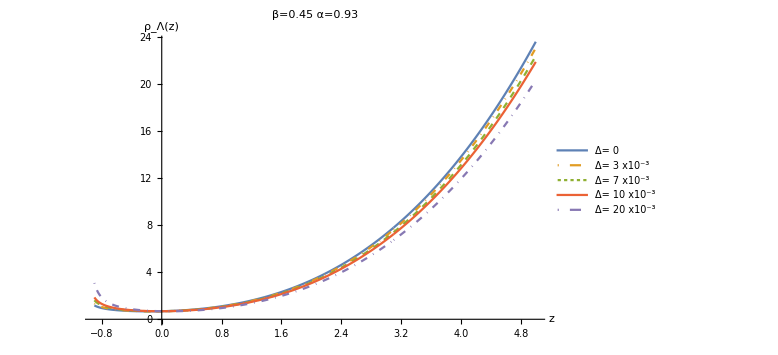

```mathematica
ListLinePlot[{dataZvsDE1,dataZvsDE2,dataZvsDE3,dataZvsDE4,dataZvsDE5}, AxesLabel->{"z","ρ_Λ(z)"},PlotRange->All,PlotStyle->styles,LabelStyle->Directive[Black,Bold,10],ImageSize->Large,PlotLabel->title,PlotLegends-> Placed[legends,{0.45,0.65}]]
```

```mathematica
DEz1=Interpolation[dataZvsDE1,Method->"Hermite"];
```

```mathematica
DEz2=Interpolation[dataZvsDE2,Method->"Hermite"];
```

```mathematica
DEz3=Interpolation[dataZvsDE3,Method->"Hermite"];
```

```mathematica
DEz4=Interpolation[dataZvsDE4,Method->"Hermite"];
```

```mathematica
DEz5=Interpolation[dataZvsDE5,Method->"Hermite"];
```

```mathematica
Subscript[P̃, Λ1]=-Subscript[ρ̃, Λ1]+ (1/3)(1+Z) ND[DEz1[z],z,Z,WorkingPrecision->40,Terms->10]; dataZvsPDE1= Transpose[{Z,Subscript[P̃, Λ1]}];
```

InterpolatingFunction::dmval: Input value {5.0005} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.001} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.0015} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Subscript[P̃, Λ2]=-Subscript[ρ̃, Λ2]+ (1/3)(1+Z) ND[DEz2[z],z,Z,WorkingPrecision->40,Terms->10]; dataZvsPDE2= Transpose[{Z,Subscript[P̃, Λ2]}];
```

InterpolatingFunction::dmval: Input value {5.0005} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.001} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.0015} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Subscript[P̃, Λ3]=-Subscript[ρ̃, Λ3]+ (1/3)(1+Z) ND[DEz3[z],z,Z,WorkingPrecision->40,Terms->10]; dataZvsPDE3= Transpose[{Z,Subscript[P̃, Λ3]}];
```

InterpolatingFunction::dmval: Input value {5.0005} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.001} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.0015} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Subscript[P̃, Λ4]=-Subscript[ρ̃, Λ4]+ (1/3)(1+Z) ND[DEz4[z],z,Z,WorkingPrecision->40,Terms->10]; dataZvsPDE4= Transpose[{Z,Subscript[P̃, Λ4]}];
```

InterpolatingFunction::dmval: Input value {5.0005} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.001} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.0015} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Subscript[P̃, Λ5]=-Subscript[ρ̃, Λ5]+ (1/3)(1+Z) ND[DEz5[z],z,Z,WorkingPrecision->40,Terms->10]; dataZvsPDE5= Transpose[{Z,Subscript[P̃, Λ5]}];
```

InterpolatingFunction::dmval: Input value {5.0005} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.001} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.0015} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Subscript[w, Λ1]=Subscript[P̃, Λ1] /Subscript[ρ̃, Λ1]; dataZvsWDE1= Transpose[{Z,Subscript[w, Λ1]}];
```

```mathematica
Subscript[w, Λ2]=Subscript[P̃, Λ2] /Subscript[ρ̃, Λ2]; dataZvsWDE2= Transpose[{Z,Subscript[w, Λ2]}];
```

```mathematica
Subscript[w, Λ3]=Subscript[P̃, Λ3] /Subscript[ρ̃, Λ3]; dataZvsWDE3= Transpose[{Z,Subscript[w, Λ3]}];
```

```mathematica
Subscript[w, Λ4]=Subscript[P̃, Λ4] /Subscript[ρ̃, Λ4]; dataZvsWDE4= Transpose[{Z,Subscript[w, Λ4]}];
```

```mathematica
Subscript[w, Λ5]=Subscript[P̃, Λ5] /Subscript[ρ̃, Λ5]; dataZvsWDE5= Transpose[{Z,Subscript[w, Λ5]}];
```

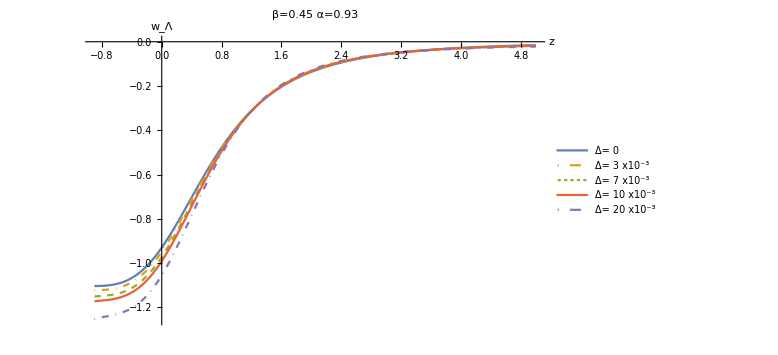

```mathematica
ListLinePlot[{dataZvsWDE1,dataZvsWDE2,dataZvsWDE3,dataZvsWDE4,dataZvsWDE5}, AxesLabel->{"z","w_Λ"},PlotRange->All,PlotLegends-> Placed[legends,{0.9,0.75}],PlotStyle->styles,LabelStyle->Directive[Black,Bold,10],ImageSize->Large,PlotLabel->title]
```

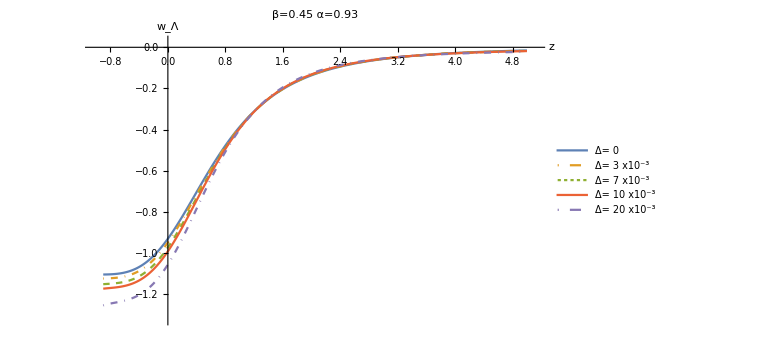

-Graphics-

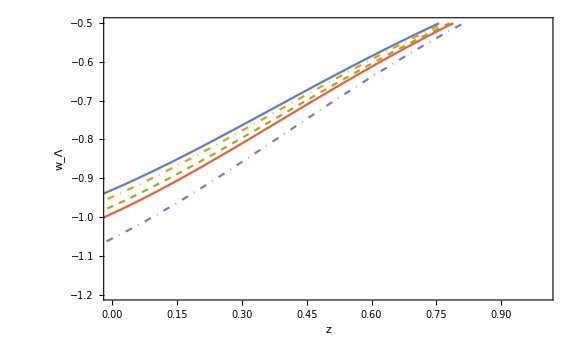

```mathematica
ListLinePlot[{dataZvsWDE1,dataZvsWDE2,dataZvsWDE3,dataZvsWDE4,dataZvsWDE5}, AxesLabel->{"z","w_Λ"},PlotRange->{{0,1},{-1.2,-0.5}},PlotStyle->styles,LabelStyle->Directive[Black,Bold,10],ImageSize->Large,Frame->True, FrameLabel->{{"w_Λ",""},{z,"w_0"}}]
```

------------------------//-------------------------------------------------//-------------------------------------------------------------//---------------------------------------------------------//--------------------------------

```mathematica
zvs=Range[0,1.5,step];
```

```mathematica
PDE1=Interpolation[dataZvsPDE1,Method->"Hermite"];                 vs21= ND[PDE1[z],z,zvs,WorkingPrecision->40,Terms->10]/(ND[DEz1[z],z,zvs,WorkingPrecision->40,Terms->10]);
```

```mathematica
PDE2=Interpolation[dataZvsPDE2,Method->"Hermite"];                 vs22= ND[PDE2[z],z,zvs,WorkingPrecision->40,Terms->10]/(ND[DEz2[z],z,zvs,WorkingPrecision->40,Terms->10]);
```

```mathematica
PDE3=Interpolation[dataZvsPDE3,Method->"Hermite"];                  vs23= ND[PDE3[z],z,zvs,WorkingPrecision->40,Terms->10]/(ND[DEz3[z],z,zvs,WorkingPrecision->40,Terms->10]);
```

```mathematica
PDE4=Interpolation[dataZvsPDE4,Method->"Hermite"];                  vs24= ND[PDE4[z],z,zvs,WorkingPrecision->40,Terms->10]/(ND[DEz4[z],z,zvs,WorkingPrecision->40,Terms->10]);
```

```mathematica
PDE5=Interpolation[dataZvsPDE5,Method->"Hermite"];                  vs25= ND[PDE5[z],z,zvs,WorkingPrecision->40,Terms->10]/(ND[DEz5[z],z,zvs,WorkingPrecision->40,Terms->10]);
```

```mathematica
plotvs2={Transpose[{zvs,Sign[vs21]vs21}],Transpose[{zvs,Sign[vs22]vs22}],Transpose[{zvs,Sign[vs23]vs23}],Transpose[{zvs,Sign[vs24]vs24}],Transpose[{zvs,Sign[vs25]vs25}]};
```

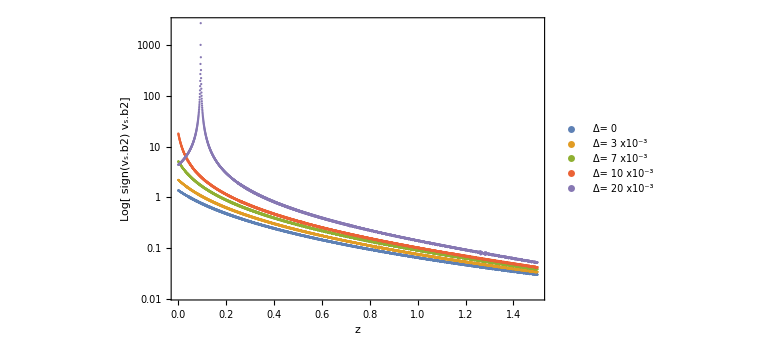

```mathematica
ListLogPlot[plotvs2, PlotRange-> All,PlotStyle->styles,LabelStyle->Directive[Black,Bold,10],ImageSize->Large,Frame->True, FrameLabel->{{"Log[ sign(v_s.b2) v_s.b2]",""},{z,title}},PlotLegends-> Placed[legends,{0.65,0.65}]]
```

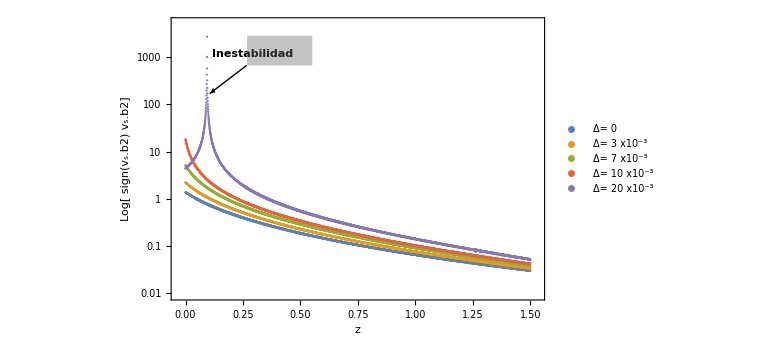

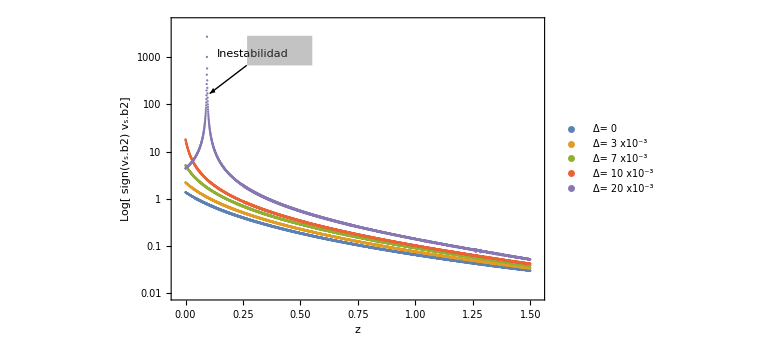

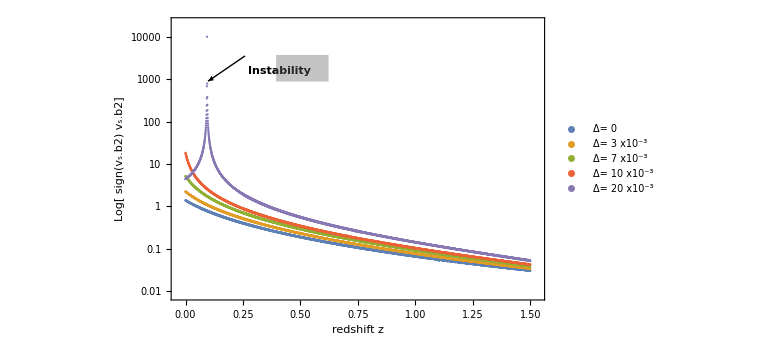

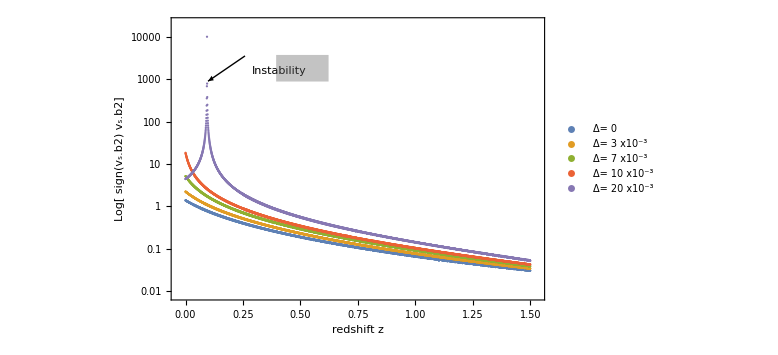

```mathematica
N[-1+Exp[-(-3)]]
```

19.0855